ClearAll

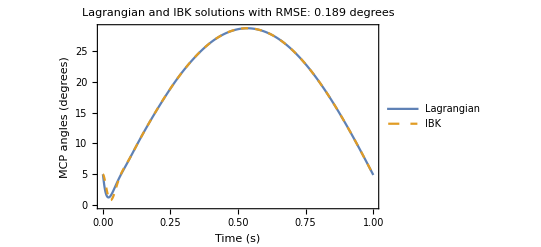

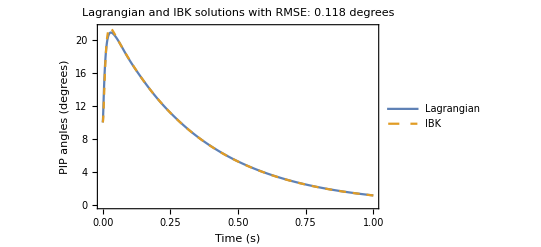

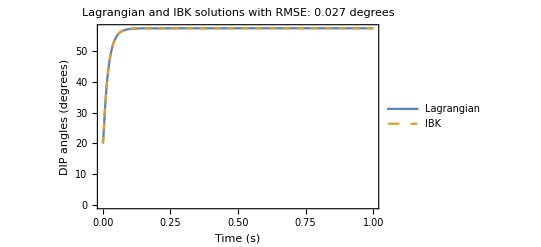

```mathematica
ClearAll

(* Parameters for Simulation *)
L1=1;
L2=0.5;
L3=0.3;
R1=0.01;
R2=0.02;
R3=0.015;
rho=1.16;
m1=Pi*rho*R1^2*L1;
m2=Pi*rho*R2^2*L2;
m3=Pi*rho*R3^2*L3;
I1=m1*(R1^2/4+L1^2/12);
I2=m2*(R2^2/4+L2^2/12);
I3=m3*(R3^2/4+L1^3/12);
K1=10;
b1=0.1;
K2=5;
b2=B1/2;
K3=1;
K4=1;
b4=0.01;
b3=B1/5;
th1eq=0;
th2eq=0;
th3eq=0;
phieq=0;
(* For IBK Simulation *)
Ib1= I1+L1^2*(m2+m3)+m1*L1^2/4;
Ib2=I2+L2^2*m3+m2*L2^2/4;
Ib3=I3+m3*L3^2/4;

(* Model Equations *)

xy1[t]=-L1/2*Cos[th1[t]];
z1[t]=-L1/2*Sin[th1[t]];
xy2[t]=-(L1*Cos[th1[t]]+L2/2*Cos[th2[t]]);
z2[t]=-(L1*Sin[th1[t]]+L2/2*Sin[th2[t]]);
xy3[t]=-(L1*Cos[th1[t]]+L2*Cos[th2[t]]+L3/2*Cos[th3[t]]);
z3[t]=-(L1*Sin[th1[t]]+L2*Sin[th2[t]]+L3/2*Sin[th3[t]]);

x1[t]=xy1[t]*Cos[phi[t]];
y1[t]=xy1[t]*Sin[phi[t]];
x2[t]=xy2[t]*Cos[phi[t]];
y2[t]=xy2[t]*Sin[phi[t]];
x3[t]=xy3[t]*Cos[phi[t]];
y3[t]=xy3[t]*Sin[phi[t]];

r1[t]=D[z1[t],t]^2+D[x1[t],t]^2+D[y1[t],t]^2;
Simplify[r1[t]];
r2[t]=D[z2[t],t]^2+D[x2[t],t]^2+D[y2[t],t]^2;
Simplify[Expand[r2[t]]];
r3[t]=D[z3[t],t]^2+D[x3[t],t]^2+D[y3[t],t]^2;
Simplify[Expand[r3[t]]];

K1a=1/2*(m1*r1[t]+m2*r2[t]+m3*r3[t]);
T=1/2*(I1*(th1'[t]^2+Cos[th1[t]]^2*phi'[t]^2)+I2*(th2'[t]^2+Cos[th2[t]]^2*phi'[t]^2)+I3*(th3'[t]^2+Cos[th3[t]]^2*phi'[t]^2));
Kt=K1a+T//FullSimplify;
Vspr=K1/2*(th1[t]-th1eq)^2+K2/2*(th2[t]-th2eq)^2+K3/2*(th3[t]-th3eq)^2+K4/2*(phi[t]-phieq)^2;
(*Vgrav=m1*g*z1[t]+m2*g*z2[t]+m3*g*z3[t];*)

V=Vspr(*+Vgrav*);
(*Lagrangian*)
L=Kt-V;

a=D[D[L,th1'[t]],t]-D[L,th1[t]]+b1*th1'[t];
a//FullSimplify;
b=D[D[L,th2'[t]],t]-D[L,th2[t]]+b2*th2'[t];
b//FullSimplify;
c=D[D[L,th3'[t]],t]-D[L,th3[t]]+b3*th3'[t];
c//FullSimplify;
d=D[D[L,phi'[t]],t]-D[L,phi[t]]+b4*phi'[t];
(* Inputs *)

T1[t_]:=5*Sin[3*t];
T2[t_]:= 2*Exp[-3*t];
T3=1;


eqns={a==T1[t],b==T2[t],c==T3,d==0};

(* Numerical Solve of Lagrangian *)

s=NDSolve[{eqns,th1[0]==5*Pi/180,th1'[0]==0,th2[0]==10*Pi/180,th2'[0]==0,th3[0]==20*Pi/180,th3'[0]==0,phi[0]==15*Pi/180,phi'[0]==0},{th1[t],th2[t],th3[t],phi[t]},{t,0,1}];

(* IBK Approximation *)

F[Im1_, Bm_, Km_,u_]:=Im1*u''[t]+Bm*u'[t]+Km*u[t];


s1=NDSolve[{{F[Ib1,b1,K1,x]==T1[t]},x[0]==5*Pi/180,x'[0]==0},{x[t]},{t,0,1}];

s2=NDSolve[{{F[Ib2,b2,K2,x]==T2[t]},x[0]==10*Pi/180,x'[0]==0},{x[t]},{t,0,1}];

s3=NDSolve[{{F[Ib3,b3,K3,x]==T3},x[0]==20*Pi/180,x'[0]==0},{x[t]},{t,0,1}];

(* Extract Lagrangian and IBK solutions *)
th1Sol = th1[t] /. s[[1]];
s1Sol = x[t] /. s1[[1]];
th2Sol=th2[t]/.s[[1]];
s2Sol=x[t]/.s2[[1]];
th3Sol=th3[t]/.s[[1]];
s3Sol=x[t]/.s3[[1]];


(* Generate the time points *)
timePoints = Range[0, 1, 0.001];

(* Evaluate th1 and s1 at each time point *)
th1Values = Table[Evaluate[th1Sol /. t -> tval]*180/Pi, {tval, timePoints}];
s1Values = Table[Evaluate[s1Sol /. t -> tval]*180/Pi, {tval, timePoints}];
rms=Sqrt[Mean[(th1Values-s1Values)^2]];

(* Plot th1 and s1 against time *)
ListLinePlot[{Transpose[{timePoints, th1Values}], Transpose[{timePoints, s1Values}]}, 
 PlotRange -> All,Frame->True, 
 FrameLabel -> {"Time (s)", "MCP angles (degrees)"}, 
 PlotLegends -> {"Lagrangian", "IBK"}, PlotStyle -> {Automatic, Dashed},PlotLabel-> StringForm["Lagrangian and IBK solutions with RMSE: `` degrees", NumberForm[rms,{Infinity, 3}]]]

(* Evaluate th2 and s2 at each time point *)
th2Values = Table[Evaluate[th2Sol /. t -> tval]*180/Pi, {tval, timePoints}];
s2Values = Table[Evaluate[s2Sol /. t -> tval]*180/Pi, {tval, timePoints}];
rms=Sqrt[Mean[(th2Values-s2Values)^2]];

(* Plot th2 and s2 against time *)
ListLinePlot[{Transpose[{timePoints, th2Values}], Transpose[{timePoints, s2Values}]}, 
 PlotRange -> All,Frame->True, 
 FrameLabel -> {"Time (s)", "PIP angles (degrees)"}, 
 PlotLegends -> {"Lagrangian", "IBK"}, PlotStyle -> {Automatic, Dashed},PlotLabel-> StringForm["Lagrangian and IBK solutions with RMSE: `` degrees", NumberForm[rms,{Infinity, 3}]]]


(* Evaluate th3 and s3 at each time point *)
th3Values = Table[Evaluate[th3Sol /. t -> tval]*180/Pi, {tval, timePoints}];
s3Values = Table[Evaluate[s3Sol /. t -> tval]*180/Pi, {tval, timePoints}];
rms=Sqrt[Mean[(th3Values-s3Values)^2]];

(* Plot th1 and s1 against time *)
ListLinePlot[{Transpose[{timePoints, th3Values}], Transpose[{timePoints, s3Values}]}, 
 PlotRange -> All,Frame->True, 
 FrameLabel -> {"Time (s)", "DIP angles (degrees)"}, 
 PlotLegends -> {"Lagrangian", "IBK"}, PlotStyle -> {Automatic, Dashed},PlotLabel-> StringForm["Lagrangian and IBK solutions with RMSE: `` degrees", NumberForm[rms,{Infinity, 3}]]]
```